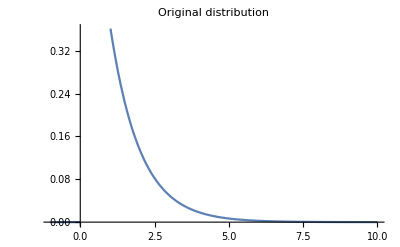

```mathematica
(*
	Simulating central limit theorem
*)
ClearAll["Global`*"]
Clear["Global`*"]
SetOptions[EvaluationNotebook[],NotebookEventActions->{"WindowClose"->FrontEndTokenExecute["DeleteGeneratedCells"]}]
$Pre=.  (*clear the prior definition for $Pre*)
echo=Function[main,Unevaluated[main]/.Set->Function[,Print@HoldForm[#=#2];#=#2,HoldFirst],HoldAll];


origDist = ExponentialDistribution[1];
pdfH[z_]:=PDF[origDist,z];
Plot[pdfH[x],{x, -1, 10},PlotLabel->"Original distribution"]

Manipulate[
	samples = Table[ RandomVariate[origDist,SampleSize],SamplesCount];
	means=Mean/@samples;
	(*{Mean[means],StandardDeviation[means]}*)

	Histogram[means,100],

	{{SampleSize,100},1,150,1,Appearance->"Labeled"},
	{{SamplesCount,1000},10,10000,10,Appearance->"Labeled"}
]
```